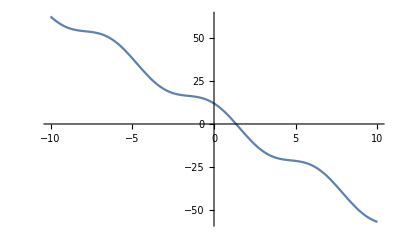

```mathematica
f[x_]=5*Cos[x]-6*x+7;
Plot[f[x],{x,-10,10}]
```

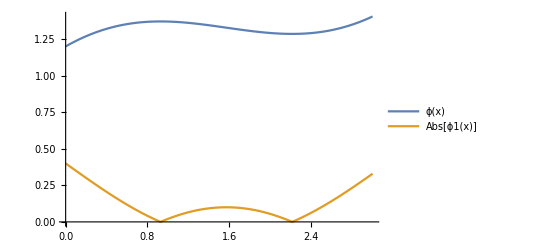

```mathematica
(*Перейдем к равносильному уравнению и подберем параметр λ и отрезок так, чтобы выполнились все условия теоремы Банаха*)
λ=-1/10;
ϕ[x_]=x-λ*f[x];
A=0;
B=3;
ϕ1[x_]=D[ϕ[x],x];
Plot[{ϕ[x],Abs[ϕ1[x]]},{x,A,B},PlotLegends->"Expressions"]
```

```mathematica
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим отрезок, на котором выполняются все условия теоремы Банаха*)
a=A;
b=B;
(*Найдем константу сжатия*)
α=MaxValue[{Abs[ϕ1[x]],a≤x≤b},x];
(*Зададим начальное приближение к корню*)
x0=a;
(*Найдем первую итерацию*)
x1=ϕ[x0];
(*Зададим переменную для хранения последовательности итерация*)
It={{x0,0},{x1,0}};
Edges={{a,b},{Min[N[ϕ[a]],N[ϕ[b]]],Max[N[ϕ[a]],N[ϕ[b]]]}};
(*Найдем количество итераций, используя априорную оценку теоремы Банаха*)
n=Floor[Log[α,ϵ*(1-α)/Abs[x1-x0]]]+1;
(*Реализцем алгоритм метода итераций*)
For[i=1,i≤n,i++,
a=Min[N[ϕ[a]],N[ϕ[b]]];
b=Max[N[ϕ[a]],N[ϕ[b]]];
x0=x1;
x1=ϕ[x0];
It=AppendTo[It,{x1,0}];
Edges=AppendTo[Edges,{Min[N[ϕ[a]],N[ϕ[b]]],Max[N[ϕ[a]],N[ϕ[b]]]}]
]
Print["Корень уравнения равен: ",N[x1]]
Print["Количество итераций равно: ",n]
Dimensions[Edges]
Edges[[10,2]]
```

Корень уравнения равен: 1.34954

Количество итераций равно: 9

{11,2}

1.34954

```mathematica
(*Выполним анимацию приближений к корню*)
G=Plot[f[x],{x,A,B},PlotStyle->Yellow];
Animate[Show[G,Plot[0,{x,Edges[[k,1]],Edges[[k,2]]},PlotStyle->Blue],Plot[0,{x,Edges[[k+1,1]],Edges[[k+1,2]]},PlotStyle->Green],ListPlot[{It[[k]]},PlotStyle->Red]],{k,1,n,1},AnimationRunning->False]
```